### Define equations

```mathematica
q = {PRv == v*bv*EIR/(bv*EIR + r),
PRc == (1-v)*bc*EIR/(bc*EIR + r),
EIR == m a^2 c (PRv + PRc) Exp[-g n]/(a c (PRv + PRc)+g)};
```

## Limits that we know and understand :

### Look at the zero vaccinations limit

```mathematica
Solve[q/.v->0, {PRv, PRc, EIR}]
```

{{PRv→0,PRc→0,EIR→0},{PRv→0,PRc→(a^2 bc c m-ⅇ^(g n) g r)/(a c (a bc m+ⅇ^(g n) r)),EIR→-(ⅇ^(-g n) (-a^2 bc c m+ⅇ^(g n) g r))/(bc (a c+g))}}

### Look at the zero effectiveness limit

```mathematica
Solve[q/.{bv->b, bc->b},{PRv,PRc, EIR}]
```

{{PRv→0,PRc→0,EIR→0},{PRv→((a^2 b c m-ⅇ^(g n) g r) v)/(a c (a b m+ⅇ^(g n) r)),PRc→-((a^2 b c m-ⅇ^(g n) g r) (-1+v))/(a c (a b m+ⅇ^(g n) r)),EIR→-(ⅇ^(-g n) (-a^2 b c m+ⅇ^(g n) g r))/(b (a c+g))}}

```mathematica
Simplify[(PRv + PRc)/.%[[2]]]
```

(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)

### Look at the perfect vaccine limit

```mathematica
Solve[q/.{bv->0},{PRv,PRc, EIR}]
```

{{PRv→0,PRc→0,EIR→0},{PRv→0,PRc→-(-a^2 bc c m+ⅇ^(g n) g r+a^2 bc c m v)/(a c (a bc m+ⅇ^(g n) r)),EIR→(ⅇ^(-g n) (-a^2 bc c m+ⅇ^(g n) g r+a^2 bc c m v))/(bc (-a c-g+a c v))}}

### Look at the 100% coverage limit

```mathematica
q/.v->1
```

{PRv==(bv EIR)/(bv EIR+r),PRc==0,EIR==(a^2 c ⅇ^(-g n) m (PRc+PRv))/(g+a c (PRc+PRv))}

```mathematica
Solve[q/.v->1,{PRv,PRc,EIR}]
```

{{PRv→0,PRc→0,EIR→0},{PRv→(a^2 bv c m-ⅇ^(g n) g r)/(a c (a bv m+ⅇ^(g n) r)),PRc→0,EIR→-(ⅇ^(-g n) (-a^2 bv c m+ⅇ^(g n) g r))/(bv (a c+g))}}

## Now solve before taking limits

The good news is that these just seem to require a little bit of massaging, rather than it being completely wrong

```mathematica
qsols = Solve[q,{PRv, PRc, EIR}];
```

### Zero vaccinations limit

```mathematica
PRv/.qsols[[3]]
Limit[PRv/.qsols[[3]],v->0]
```

v-(r v)/(r+1/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g))bv (a^2 bc bv c m-a bc c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+a bc c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 bc bv c m+a bc c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r-a bc c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bc c m r+ⅇ^(g n) g r^2+a^2 bc c m r v-a^2 bv c m r v))))

0

```mathematica
PRc/.qsols[[3]]
FullSimplify[Limit[PRc/.qsols[[3]],v->0],Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
```

1-v-r/(r+1/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g))bc (a^2 bc bv c m-a bc c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+a bc c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 bc bv c m+a bc c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r-a bc c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bc c m r+ⅇ^(g n) g r^2+a^2 bc c m r v-a^2 bv c m r v))))+(r v)/(r+1/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g))bc (a^2 bc bv c m-a bc c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+a bc c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 bc bv c m+a bc c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r-a bc c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bc c m r+ⅇ^(g n) g r^2+a^2 bc c m r v-a^2 bv c m r v))))

Piecewise[{{bc/(bc-bv), a^2 bc bv c m+ⅇ^(g n) (a bc c+(bc-bv) g) r<0}, {(a^2 bc c m-ⅇ^(g n) g r)/(a^2 bc c m+a c ⅇ^(g n) r), True}}]

```mathematica
(* The alternative solution is incorrect, on account of bc>bv, forcing the LHS to be >0 *)
```

### Zero effectiveness limit

```mathematica
PRv/.qsols[[3]]
FullSimplify[PRv/.qsols[[3]]/.{bc->b,bv->b},Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
```

v-(r v)/(r+1/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g))bv (a^2 bc bv c m-a bc c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+a bc c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 bc bv c m+a bc c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r-a bc c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bc c m r+ⅇ^(g n) g r^2+a^2 bc c m r v-a^2 bv c m r v))))

(a^2 b c m v-ⅇ^(g n) g r v)/(a^2 b c m+a c ⅇ^(g n) r)

```mathematica
PRc/.qsols[[3]]
FullSimplify[PRc/.qsols[[3]]/.{bc->b,bv->b},Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
```

1-v-r/(r+1/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g))bc (a^2 bc bv c m-a bc c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+a bc c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 bc bv c m+a bc c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r-a bc c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bc c m r+ⅇ^(g n) g r^2+a^2 bc c m r v-a^2 bv c m r v))))+(r v)/(r+1/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g))bc (a^2 bc bv c m-a bc c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+a bc c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 bc bv c m+a bc c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r-a bc c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bc c m r+ⅇ^(g n) g r^2+a^2 bc c m r v-a^2 bv c m r v))))

-((a^2 b c m-ⅇ^(g n) g r) (-1+v))/(a c (a b m+ⅇ^(g n) r))

### Perfect vaccine limit

```mathematica
FullSimplify[PRv/.qsols[[3]]/.{bc->b},Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
Simplify[Limit[%,bv->0],Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,v>0,v<1,bc>bv}]
```

v-(2 b ⅇ^(g n) (a c+g) r v)/(a^2 b bv c m+(b-bv) ⅇ^(g n) g r+a c ⅇ^(g n) r (b+b v-bv v)+√(-4 b bv ⅇ^(g n) (a c+g) r (ⅇ^(g n) g r+a^2 c m (b (-1+v)-bv v))+(a^2 b bv c m-ⅇ^(g n) r ((b+bv) g+a c (b-b v+bv v)))^2))

0

```mathematica
FullSimplify[PRc/.qsols[[3]]/.{bc->b},Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
Simplify[Limit[%,bv->0],Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,v>0,v<1,bc>bv}]
```

-1/(2 a (b-bv) c (a b m+ⅇ^(g n) r))(a^2 b c m (bv+2 b (-1+v)-2 bv v)+ⅇ^(g n) r ((b-bv) g+a c (b (-1+v)-bv v))+√(-4 b bv ⅇ^(g n) (a c+g) r (ⅇ^(g n) g r+a^2 c m (b (-1+v)-bv v))+(a^2 b bv c m-ⅇ^(g n) r ((b+bv) g+a c (b-b v+bv v)))^2))

-(ⅇ^(g n) g r+a^2 b c m (-1+v))/(a c (a b m+ⅇ^(g n) r))

```mathematica
FullSimplify[EIR/.qsols[[3]]/.{bc->b},Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
Simplify[Limit[%,bv->0],Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,v>0,v<1,bc>bv}]
```

1/(2 b bv (a c+g))ⅇ^(-g n) (a^2 b bv c m-(b+bv) ⅇ^(g n) g r+a c ⅇ^(g n) r (b (-1+v)-bv v)+√(-4 b bv ⅇ^(g n) (a c+g) r (ⅇ^(g n) g r+a^2 c m (b (-1+v)-bv v))+(a^2 b bv c m-ⅇ^(g n) r ((b+bv) g+a c (b-b v+bv v)))^2))

Indeterminate

### 100% coverage limit

```mathematica
PRc/.qsols[[3]]/.v->1
```

0

```mathematica
PRv/.qsols[[3]]/.v->1
```

1-r/(r+(bv (a^2 bc bv c m-a bv c ⅇ^(g n) r-bc ⅇ^(g n) g r-bv ⅇ^(g n) g r+√((-a^2 bc bv c m+a bv c ⅇ^(g n) r+bc ⅇ^(g n) g r+bv ⅇ^(g n) g r)^2-4 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g) (-a^2 bv c m r+ⅇ^(g n) g r^2))))/(2 (a bc bv c ⅇ^(g n)+bc bv ⅇ^(g n) g)))

```mathematica
FullSimplify[PRv/.qsols[[3]]/.{v->1},Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
```

Piecewise[{{-bv/(bc-bv), a^2 bc bv c m+ⅇ^(g n) (a bv c+(-bc+bv) g) r<0}, {(a^2 bv c m-ⅇ^(g n) g r)/(a^2 bv c m+a c ⅇ^(g n) r), True}}]

## Effect size, breaking down into personal protection as well as individual reduction in EIR

The change in EIR is the effect size that we will need to use.  The incidence rate in our model is b*EIR.  Both terms change in the vaccinated population, and only one of the terms changes in the unvaccinated population

```mathematica
(* EIR prior to vaccination *)
FullSimplify[EIR/.qsols[[3]]/.v->0, Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
(a^2 bc c ⅇ^(-g n) m-g r)/(a bc c+bc g)
```

Piecewise[{{-r/bv, a^2 bc bv c m+ⅇ^(g n) (a bc c+(bc-bv) g) r<0}, {(a^2 bc c ⅇ^(-g n) m-g r)/(a bc c+bc g), True}}]

(a^2 bc c ⅇ^(-g n) m-g r)/(a bc c+bc g)

```mathematica
(* After vaccination *)
(* Did try to simplify this more - it didn't work *)
FullSimplify[EIR/.qsols[[3]], Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
```

1/(2 bc bv (a c+g))ⅇ^(-g n) (a^2 bc bv c m-(bc+bv) ⅇ^(g n) g r+a c ⅇ^(g n) r (bc (-1+v)-bv v)+√(-4 bc bv ⅇ^(g n) (a c+g) r (ⅇ^(g n) g r+a^2 c m (bc (-1+v)-bv v))+(a^2 bc bv c m-ⅇ^(g n) r ((bc+bv) g+a c (bc-bc v+bv v)))^2))

```mathematica
(* The ratio of after/before *)
Subscript[EIR, ratio]=1/(a^2 bc c ⅇ^(-g n) m-g r)1/(2 bv)(a^2 bc  c m ⅇ^(-g n) bv-(bc+bv) g r-a c r ((1-v)(bc-bv )+bv)+ⅇ^(-g n) √(-4 bc bv ⅇ^(g n) (a c+g) r (ⅇ^(g n) g r+a^2 c m (bc (-1+v)-bv v))+(a^2 bc bv c m-ⅇ^(g n) r ((bc+bv) g+a c (bc-bc v+bv v)))^2));
```

### Plotting EIR ratio as the vaccine coverage and efficacy change

```mathematica
mvalue =Solve[.2==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}][[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

The incidence is bEIR.  For the vaccinated population, both b and EIR change.  

There’s an additional factor of bv that increases the effect size.

```mathematica
Plot3D[(bv/bc *Subscript[EIR, ratio])/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalue,{v,0,1},{bv,0,.55},
PlotRange->{0,1},
AxesLabel->{"v - Vaccine Coverage","bv - Efficiency after Vaccine"}]
```

-Graphics3D-

The incidence is bEIR.  For the control population, only b changes.

Note that when bv=.55 or v=0, we have no effect and the ratio is 1.  Otherwise, the ratio of EIR_after to EIR_beforegoes below 1.  It starts to run to 0 because eventually EIR_after also hits 0 when either v is large enough or bv is small enough.

```mathematica
Plot3D[Subscript[EIR, ratio]/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalue,{v,0,1},{bv,0,.55},
PlotRange->{0,1},
AxesLabel->{"v - Vaccine Coverage","bv - Efficiency after Vaccine"}]
```

-Graphics3D-

### Trying to solve for R_c

Is there a way we can write down the R_0 for the case of interventions ie R_c 
Answer: not really?  At least, it's not at all obvious

But: we can try calibrating to m and then plotting vs. bv - there should be a point where everything goes to zero?

```mathematica
FullSimplify[PRc/.qsols[[3]]/.v->0, Assumptions->{a>0, bc>0, bv>0, c>0, m>0, g>0, n>0, r>0,b>0,bc>bv}]
```

Piecewise[{{bc/(bc-bv), a^2 bc bv c m+ⅇ^(g n) (a bc c+(bc-bv) g) r<0}, {(a^2 bc c m-ⅇ^(g n) g r)/(a^2 bc c m+a c ⅇ^(g n) r), True}}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{m→0.37573}

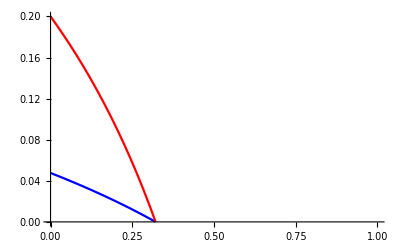

```mathematica
mvalue =Solve[.2==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}][[1]];
mvalue
Show[{Plot[PRv/v/.qsols[[3]]/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55,bv->.55*.2}/.mvalue,{v,0,1},PlotRange->{0,.2},PlotStyle->{Blue}],
Plot[PRc/(1-v)/.qsols[[3]]/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55,bv->.55*.2}/.mvalue,{v,0,1},PlotRange->{0,.2},PlotStyle->{Red}]}]
```

```mathematica
(* This let's us solve for where we get to 0, but still there really isn't an order parameter that falls out of this...
Note that the two tables are equal, meaning that the order parameter does exist.
There has to be a way of numerically backing out Subscript[R, c] but I can't remember it right now*)
Table[NSolve[0==PRv/v/.qsols[[3]]/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55,bv->.55*i}/.mvalue,v][[1]][[1,2]],{i,0.01,1,.01}]
Table[NSolve[0==PRc/(1-v)/.qsols[[3]]/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55,bv->.55*i}/.mvalue,v][[1]][[1,2]],{i,0.01,1,.01}]
```

{0.259709,0.26236,0.265064,0.267825,0.270645,0.273524,0.276465,0.27947,0.282541,0.28568,0.28889,0.292173,0.295531,0.298968,0.302485,0.306086,0.309774,0.313552,0.317423,0.32139,0.325459,0.329631,0.333912,0.338306,0.342817,0.347449,0.352209,0.357101,0.36213,0.367303,0.372627,0.378106,0.38375,0.389564,0.395558,0.401738,0.408115,0.414697,0.421496,0.428521,0.435784,0.443297,0.451074,0.459129,0.467477,0.476134,0.485118,0.494447,0.504142,0.514225,0.524719,0.535651,0.547048,0.55894,0.571361,0.584346,0.597936,0.612172,0.627103,0.642781,0.659263,0.676612,0.694898,0.714201,0.734607,0.756213,0.779128,0.803476,0.829395,0.857041,0.886594,0.918258,0.952268,0.988894,1.02845,1.0713,1.11788,1.16869,1.22434,1.28556,1.35322,1.4284,1.51243,1.60695,1.71408,1.83652,1.97779,2.1426,2.33739,2.57112,2.8568,3.2139,3.67303,4.28521,5.14225,6.42781,8.57041,12.8556,25.7112,7.85962×10^15}

{0.259709,0.26236,0.265064,0.267825,0.270645,0.273524,0.276465,0.27947,0.282541,0.28568,0.28889,0.292173,0.295531,0.298968,0.302485,0.306086,0.309774,0.313552,0.317423,0.32139,0.325459,0.329631,0.333912,0.338306,0.342817,0.347449,0.352209,0.357101,0.36213,0.367303,0.372627,0.378106,0.38375,0.389564,0.395558,0.401738,0.408115,0.414697,0.421496,0.428521,0.435784,0.443297,0.451074,0.459129,0.467477,0.476134,0.485118,0.494447,0.504142,0.514225,0.524719,0.535651,0.547048,0.55894,0.571361,0.584346,0.597936,0.612172,0.627103,0.642781,0.659263,0.676612,0.694898,0.714201,0.734607,0.756213,0.779128,0.803476,0.829395,0.857041,0.886594,0.918258,0.952268,0.988894,1.02845,1.0713,1.11788,1.16869,1.22434,1.28556,1.35322,1.4284,1.51243,1.60695,1.71408,1.83652,1.97779,2.1426,2.33739,2.57112,2.8568,3.2139,3.67303,4.28521,5.14225,6.42781,8.57041,12.8556,25.7112,7.85962×10^15}

## Procedure for calculating bEIR effect sizes

Let’s work in a particular spot in Bioko - area 219
Baseline pfpr = .1315
Population = 3185

```mathematica
(* 1. Calibrate m to baseline *)
pfpr = .1315;
mvalue =Solve[pfpr==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}][[1]];
m/.mvalue
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.337633

0.00137646

To work out how EIR changes we need to specify coverage and vaccine efficacy
• We will fix the number of people vaccinated - say at 200
• We will also fix the population denominator - the number of people within the “length scale of transmission”
• We can then solve for how PRv changes, but also solve for how EIR changes
• bv/bc is the personal protective efficacy
• EIR_after/ EIR_baseline is the additional indirect effect due to reducing transmission locally

Sanaria wants:
• Very high coverage
• Very high personal protective efficacy, if it works - 100%
• But it only works in 40% of people
This splits the vaccinated population into two groups, both of which experience the same change in EIR but different changes to b
In fact, because bv→0 in the group of people for whom the vaccine works, we will see EIR reduced to zero for that group.  But the EIR should change for the others as well - we can perhaps see the vaccine’s effects on reducing incidence in the rest of the population
(What’s tricky about this in practice is that we don’t actually know for which vaccinees the vaccine will work.  Somehow we’ll need to measure the effect size among all of the people in the treatment cohort?  How does this appear mathematically?) 

There are three population numbers that I care about
1. The total population living within the length scale of transmission - “denominator”
2. The total number of people vaccinated
3. The total number of vaccinated people for whom the vaccine works

```mathematica
(* 3. Work out how EIR changes, by specifying coverage, efficacy *)
(* Coverage *)
Subscript[n, vac]=200;
Subscript[n, tot]= 3185;
Subscript[v, vac]=Subscript[n, vac]/Subscript[n, tot];
Subscript[b, eff] = 0.01; (* 100% effective *)
ϵ = 0.4; (* Fraction of those vaccinated for whom it is effective *)
```

```mathematica
EIR/.qsols[[3]]/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalue/.{bv->Subscript[b, eff]}/.{v->Subscript[v, vac]}
```

0.000903056

# Graveyard

## Keeping v constant, what is the size of the indirect effect as bv changes?

```mathematica
qsols[[3,1]]/.bc->b
```

PRv→v-(r v)/(r+1/(2 (a b bv c ⅇ^(g n)+b bv ⅇ^(g n) g))bv (a^2 b bv c m-a b c ⅇ^(g n) r-b ⅇ^(g n) g r-bv ⅇ^(g n) g r+a b c ⅇ^(g n) r v-a bv c ⅇ^(g n) r v+√((-a^2 b bv c m+a b c ⅇ^(g n) r+b ⅇ^(g n) g r+bv ⅇ^(g n) g r-a b c ⅇ^(g n) r v+a bv c ⅇ^(g n) r v)^2-4 (a b bv c ⅇ^(g n)+b bv ⅇ^(g n) g) (-a^2 b c m r+ⅇ^(g n) g r^2+a^2 b c m r v-a^2 bv c m r v))))

```mathematica
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};
```

```mathematica
FullSimplify[qsols[[3]]/.bv->b/.bc->b/.v->0,Assumptions->{a>0, b>0, c>0, m>0, g>0,n>0,r>0}]
FullSimplify[qsols[[3]]/.bv->b/.bc->b/.v->0,Assumptions->{a>0, b>0, c>0, m>0, g>0,n>0,r>0}]/.vars
```

{PRv→0,PRc→(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r),EIR→(a^2 b c ⅇ^(-g n) m-g r)/(a b c+b g)}

{PRv→0,PRc→(-19.8334+0.010935 b m)/(7.62385+0.010935 b m),EIR→(6.85586 (-0.000526803+2.90449×10^-7 b m))/b}

```mathematica
mvalues =Table[Solve[i/10.==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}],{i,1,9}];
```

### PR before intervention = 0.1

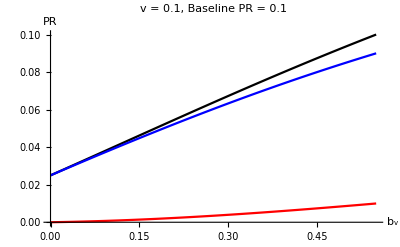

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[1,1,1]]/.v->.1;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.1},PlotLabel->"v = 0.1, Baseline PR = 0.1",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

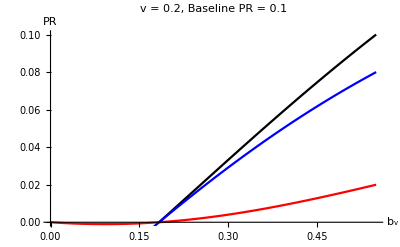

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[1,1,1]]/.v->.2;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.1},PlotLabel->"v = 0.2, Baseline PR = 0.1",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

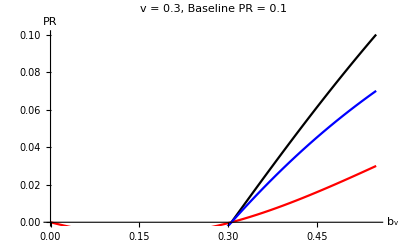

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[1,1,1]]/.v->.3;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.1},PlotLabel->"v = 0.3, Baseline PR = 0.1",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

### PR before intervention = 0.3

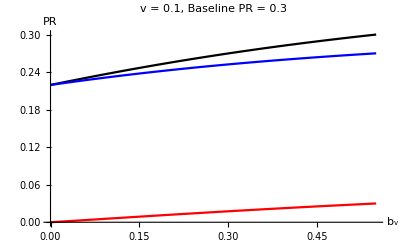

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.v->.1;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"v = 0.1, Baseline PR = 0.3",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

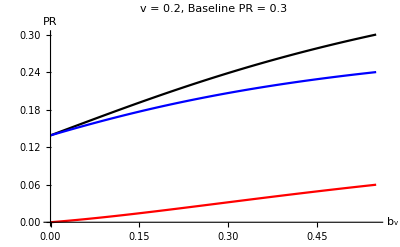

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.v->.2;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"v = 0.2, Baseline PR = 0.3",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

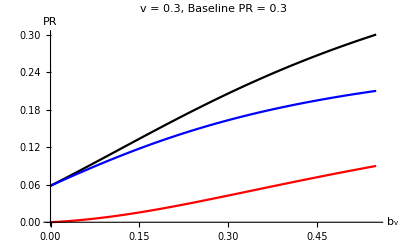

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.v->.3;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"v = 0.3, Baseline PR = 0.3",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

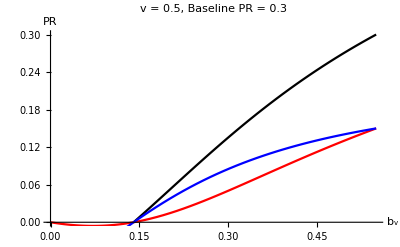

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.v->.5;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"v = 0.5, Baseline PR = 0.3",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

### PR before intervention = 0.5

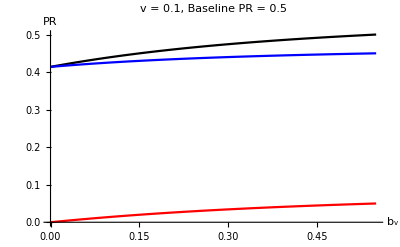

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.1;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.1, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

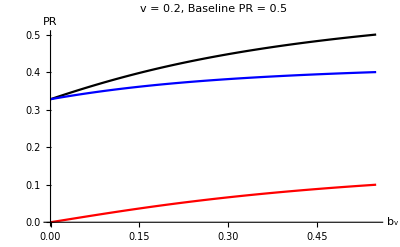

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.2;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.2, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

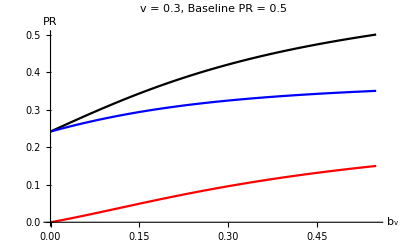

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.3;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.3, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

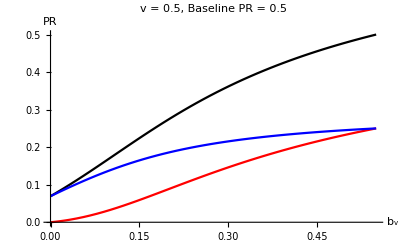

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.5;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.5, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

### PR before intervention = 0.5

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.1;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.1, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

-Graphics-

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.2;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.2, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

-Graphics-

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.3;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.3, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

-Graphics-

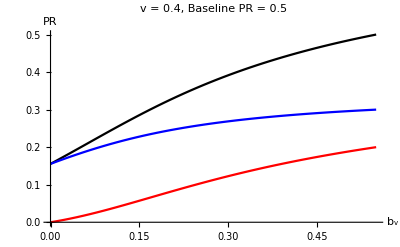

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.4;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.4, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

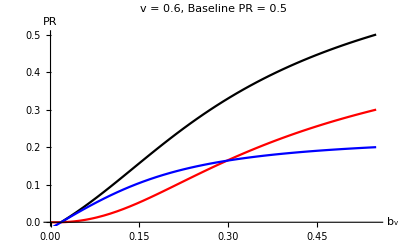

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.6;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.6, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

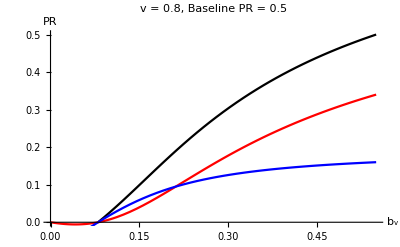

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.v->.68;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"v = 0.8, Baseline PR = 0.5",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

### PR before intervention = 0.7

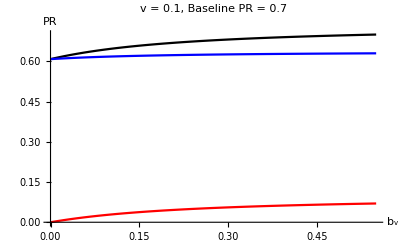

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.v->.1;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"v = 0.1, Baseline PR = 0.7",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

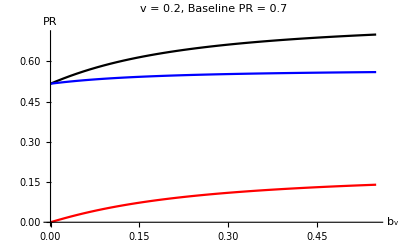

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.v->.2;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"v = 0.2, Baseline PR = 0.7",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

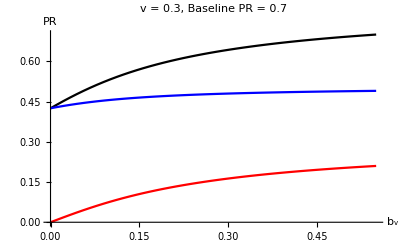

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.v->.3;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"v = 0.3, Baseline PR = 0.7",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

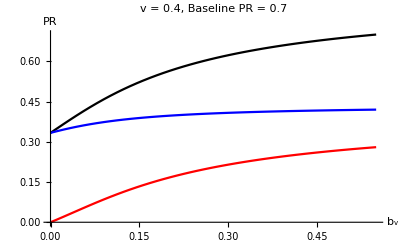

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.v->.4;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"v = 0.4, Baseline PR = 0.7",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

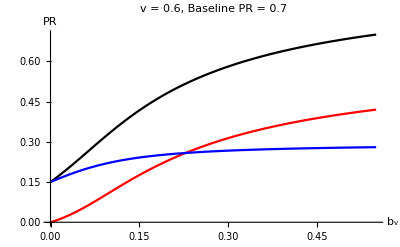

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.v->.6;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"v = 0.6, Baseline PR = 0.7",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

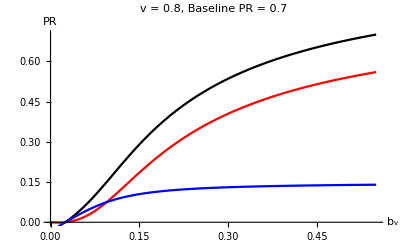

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.v->.8;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"v = 0.8, Baseline PR = 0.7",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

### PR before intervention = 0.9

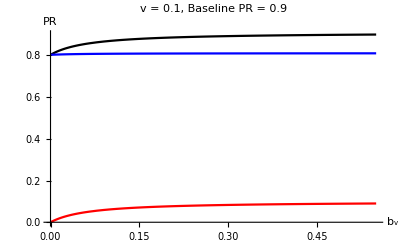

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.1;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.1, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

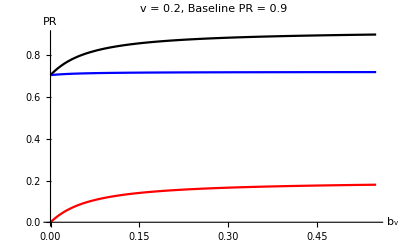

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.2;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.2, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

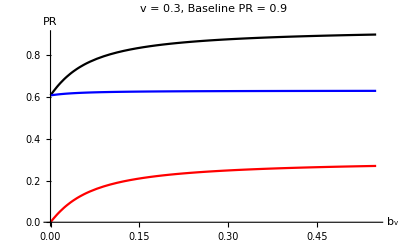

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.3;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.3, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

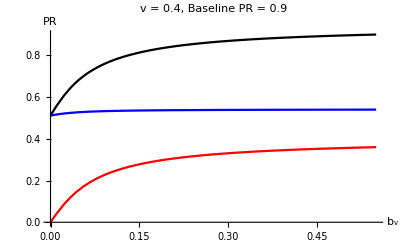

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.4;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.4, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

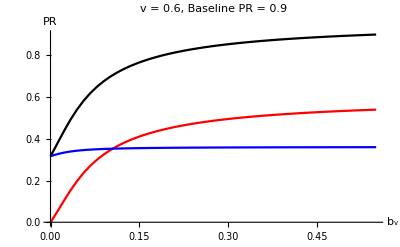

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.6;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.6, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

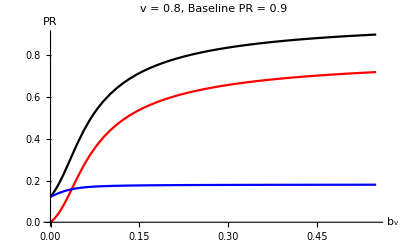

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.8;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.8, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

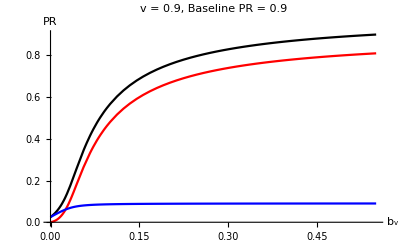

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[9,1,1]]/.v->.9;
prvplot =Plot[PRv/.vconst,{bv,0,.55},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{bv,0,.55}, PlotStyle->Blue,PlotRange->{0,.9}];
prtotal=Plot[(PRc+PRv)/.vconst,{bv,0,.55},PlotStyle->Black,PlotRange->{0,0.9},PlotLabel->"v = 0.9, Baseline PR = 0.9",
AxesLabel->{"b_v","PR"}];

Show[prtotal,prvplot, prcplot]
```

## Keeping bv constant, what is the size of the indirect effect as v changes?

```mathematica
mvalues =Table[Solve[i/10.==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}],{i,1,9}];
```

### PR before intervention = 0.1

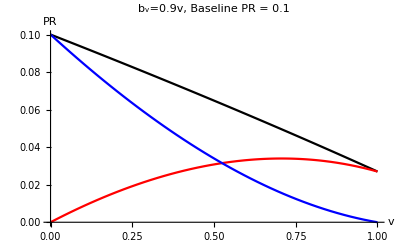

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[1,1,1]]/.bv->.9*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.1},PlotLabel->"b_v=0.9v, Baseline PR = 0.1",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

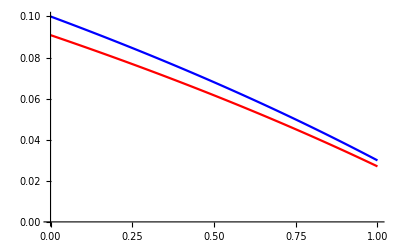

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.1},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.1},PlotStyle->Blue];
Show[prvplot,prcplot]
```

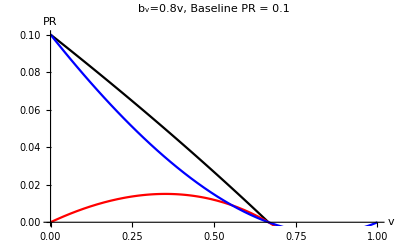

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[1,1,1]]/.bv->.8*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.1},PlotLabel->"b_v=0.8v, Baseline PR = 0.1",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

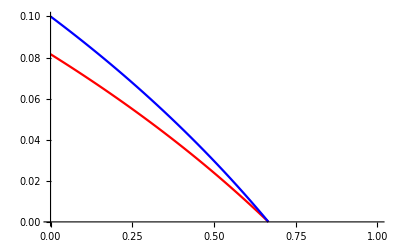

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.1},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.1},PlotStyle->Blue];
Show[prvplot,prcplot]
```

### PR before intervention = 0.3

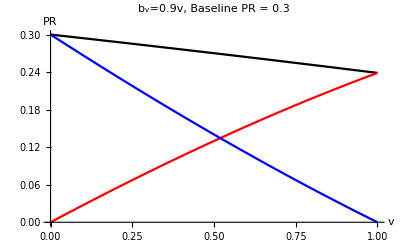

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.bv->.9*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"b_v=0.9v, Baseline PR = 0.3",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

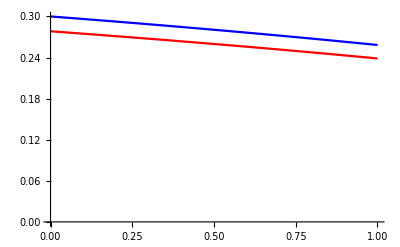

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Blue];
Show[prvplot,prcplot]
```

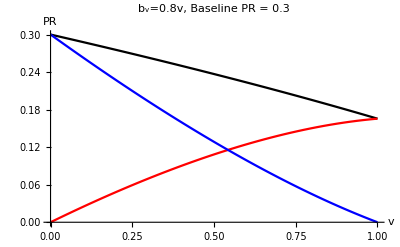

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.bv->.8*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"b_v=0.8v, Baseline PR = 0.3",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

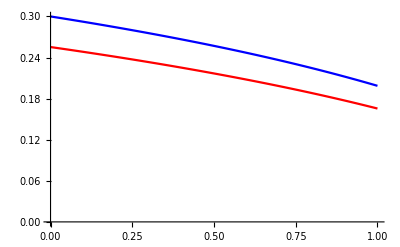

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Blue];
Show[prvplot,prcplot]
```

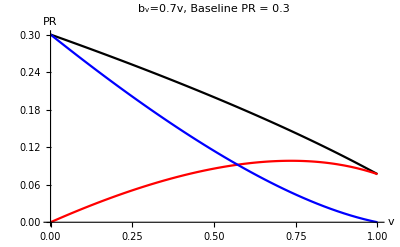

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.bv->.7*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"b_v=0.7v, Baseline PR = 0.3",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

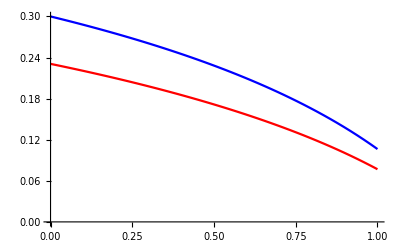

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Blue];
Show[prvplot,prcplot]
```

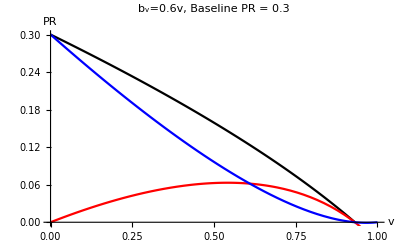

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[3,1,1]]/.bv->.6*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.3},PlotLabel->"b_v=0.6v, Baseline PR = 0.3",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

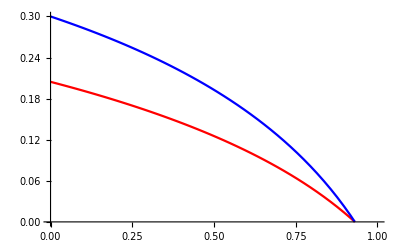

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.3},PlotStyle->Blue];
Show[prvplot,prcplot]
```

### PR before intervention = 0.5

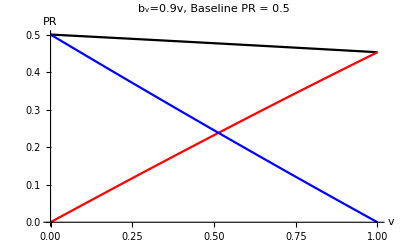

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.bv->.9*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"b_v=0.9v, Baseline PR = 0.5",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

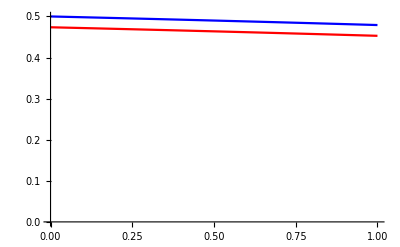

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Blue];
Show[prvplot,prcplot]
```

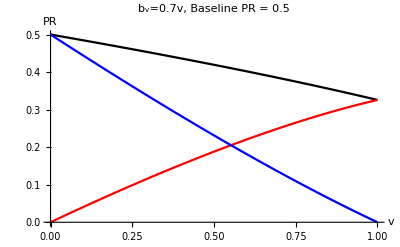

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.bv->.7*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"b_v=0.7v, Baseline PR = 0.5",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

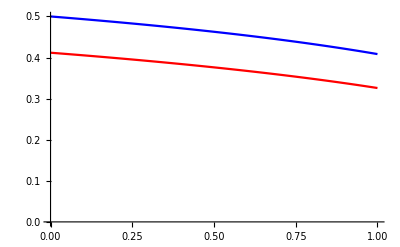

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Blue];
Show[prvplot,prcplot]
```

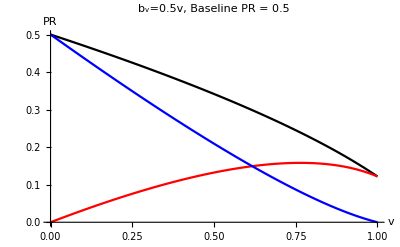

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.bv->.5*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"b_v=0.5v, Baseline PR = 0.5",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

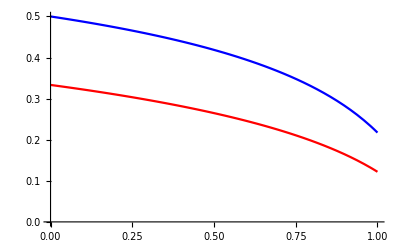

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Blue];
Show[prvplot,prcplot]
```

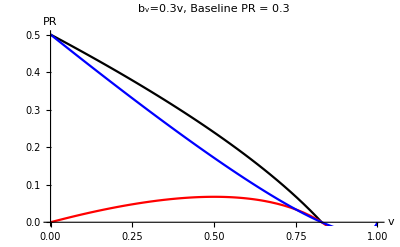

```mathematica
(* bv = 0.3*b, PR = 0.5 *)
vconst =qsols[[3]]/.vars/.mvalues[[5,1,1]]/.bv->.3*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.5},PlotLabel->"b_v=0.3v, Baseline PR = 0.3",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

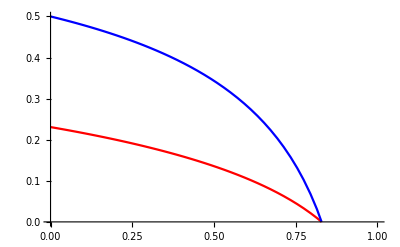

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.5},PlotStyle->Blue];
Show[prvplot,prcplot]
```

### PR before intervention = 0.7

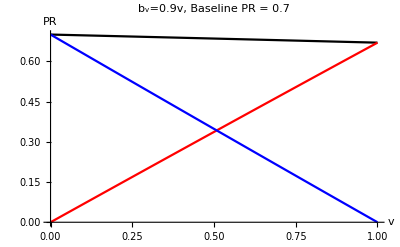

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.bv->.9*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"b_v=0.9v, Baseline PR = 0.7",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

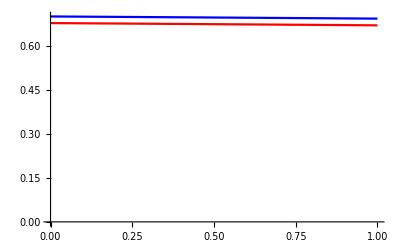

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Blue];
Show[prvplot,prcplot]
```

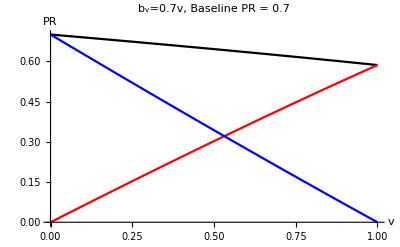

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.bv->.7*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"b_v=0.7v, Baseline PR = 0.7",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

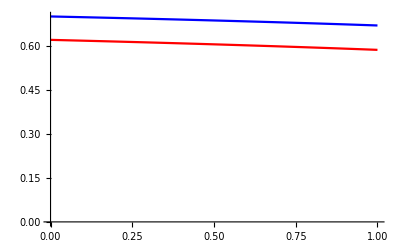

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Blue];
Show[prvplot,prcplot]
```

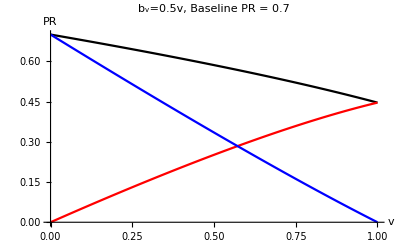

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.bv->.5*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"b_v=0.5v, Baseline PR = 0.7",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

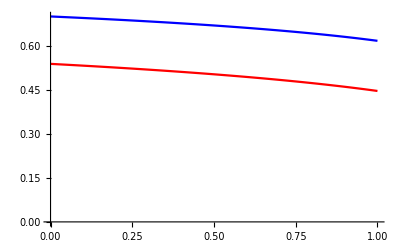

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Blue];
Show[prvplot,prcplot]
```

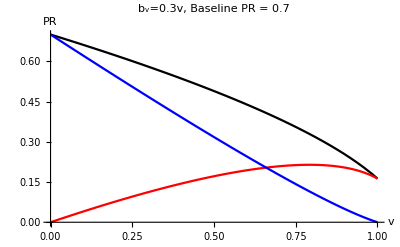

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.bv->.3*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"b_v=0.3v, Baseline PR = 0.7",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

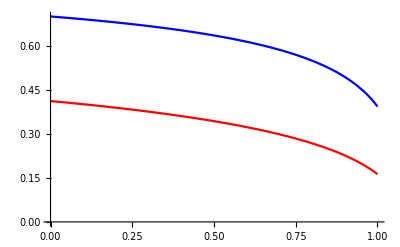

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Blue];
Show[prvplot,prcplot]
```

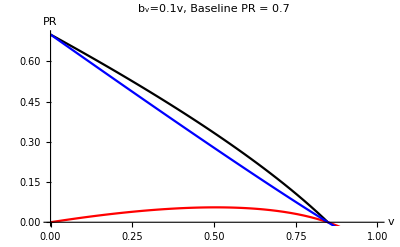

```mathematica
vconst =qsols[[3]]/.vars/.mvalues[[7,1,1]]/.bv->.1*.55;
prvplot =Plot[PRv/.vconst,{v,0,1},PlotStyle->Red];
prcplot =Plot[PRc/.vconst,{v,0,1}, PlotStyle->Blue];
prtotal=Plot[(PRc+PRv)/.vconst,{v,0,1},PlotStyle->Black,PlotRange->{0,0.7},PlotLabel->"b_v=0.1v, Baseline PR = 0.7",
AxesLabel->{"v","PR"}];
Show[prtotal,prvplot, prcplot]
```

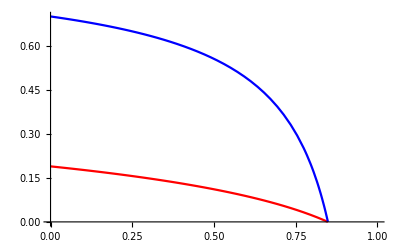

```mathematica
prvplot = Plot[PRv/v/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Red];
prcplot = Plot[PRc/(1-v)/.vconst,{v,0,1},PlotRange->{0,0.7},PlotStyle->Blue];
Show[prvplot,prcplot]
```

## For fun: 3d plots, varying both v and bv

```mathematica
mvalues =Table[Solve[i/10.==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}],{i,1,9}];
```

```mathematica
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};
```

```mathematica
PRc/.(qsols[[3]]/.vars)
```

1-v-0.005/(0.005+1/bv 1.07572 (-0.00127821-0.00167873 bv+0.00601425 bv m+0.000354912 v-0.000645294 bv v+√((0.00127821+0.00167873 bv-0.00601425 bv m-0.000354912 v+0.000645294 bv v)^2-1.02257 bv (8.39364×10^-6-0.0000300713 m+0.0000300713 m v-0.000054675 bv m v))))+(0.005 v)/(0.005+1/bv 1.07572 (-0.00127821-0.00167873 bv+0.00601425 bv m+0.000354912 v-0.000645294 bv v+√((0.00127821+0.00167873 bv-0.00601425 bv m-0.000354912 v+0.000645294 bv v)^2-1.02257 bv (8.39364×10^-6-0.0000300713 m+0.0000300713 m v-0.000054675 bv m v))))

### Baseline PR = 0.1

```mathematica
Plot3D[PRc/.(qsols[[3]]/.vars)/.mvalues[[1,1,1]],{v,0,1},{bv,0,.55},
PlotRange->{{0,1},{0,.55},{0,.1}},
AxesLabel->{"v","b_v"}]
```

-Graphics3D-

```mathematica
Plot3D[PRv/.(qsols[[3]]/.vars)/.mvalues[[1,1,1]],{v,0,1},{bv,0,.55},
PlotRange->{{0,1},{0,.55},{0,.1}},
AxesLabel->{"v","b_v"}]
```

-Graphics3D-

### Baseline PR = 0.3

```mathematica
Plot3D[PRc/.(qsols[[3]]/.vars)/.mvalues[[3,1,1]],{v,0,1},{bv,0,.55},
PlotRange->{{0,1},{0,.55},{0,.3}},
AxesLabel->{"v","b_v"}]
```

-Graphics3D-

```mathematica
Plot3D[PRv/.(qsols[[3]]/.vars)/.mvalues[[3,1,1]],{v,0,1},{bv,0,.55},
PlotRange->{{0,1},{0,.55},{0,.3}},
AxesLabel->{"v","b_v"}]
```

-Graphics3D-

### Baseline PR = 0.5

```mathematica
Plot3D[PRc/.(qsols[[3]]/.vars)/.mvalues[[5,1,1]],{v,0,1},{bv,0,.55},
PlotRange->{{0,1},{0,.55},{0,.5}},
AxesLabel->{"v","b_v"}]
```

-Graphics3D-

```mathematica
Plot3D[PRv/.(qsols[[3]]/.vars)/.mvalues[[5,1,1]],{v,0,1},{bv,0,.55},
PlotRange->{{0,1},{0,.55},{0,.5}},
AxesLabel->{"v","b_v"}]
```

-Graphics3D-

### Lessons

Overall lessons include :
- In order for PR to be reduced to 0 in both populations, we need to have both high coverage (v) and low vaccinated biting efficiency (b_v)
- For constant v, decreasing bv does lead to a quantifiable decrease in PR among the control group.  Really, though, those changes are marginal unless bv is very small and v is large

## Create a figure, showing how the total (and indirect) effects change as total population increases and coverage decreases

```mathematica
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};
```

```mathematica
(* And here is the m parameter prior to intervention *)
mvalue =Solve[.1 ==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.vars/.b->.55,m][[1]][[1]];
```

```mathematica
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}]
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}]
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}]
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}]
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]
```

0.

0.0286634

0.0759914

0.0917739

0.0975094

```mathematica
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}]
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}]
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}]
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}]
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]
```

0

0.0108656

0.00646917

0.00243117

0.000757356

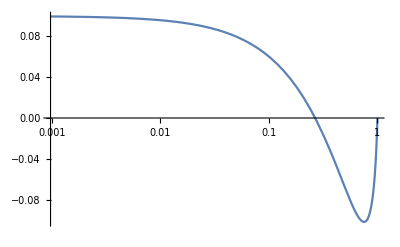

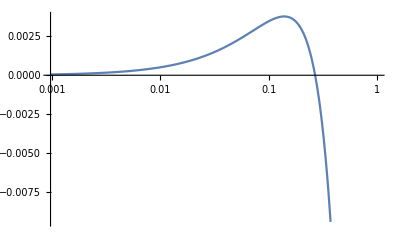

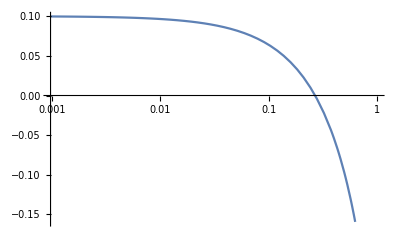

```mathematica
LogLinearPlot[PRc/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,{v,0,1}]
LogLinearPlot[PRv/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,{v,0,1}]
LogLinearPlot[(PRv+PRc)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,{v,0,1}]
```

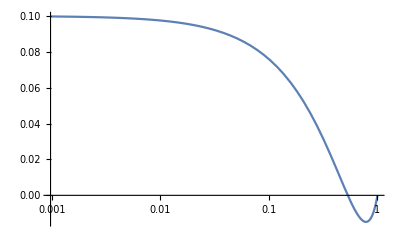

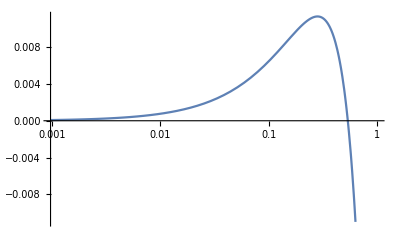

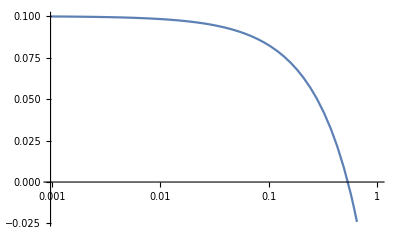

```mathematica
LogLinearPlot[PRc/.qsols[[3]]/.vars/.mvalue/.bv->.55*.75,{v,0,1}]
LogLinearPlot[PRv/.qsols[[3]]/.vars/.mvalue/.bv->.55*.75,{v,0,1}]
LogLinearPlot[(PRv+PRc)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.75,{v,0,1}]
```

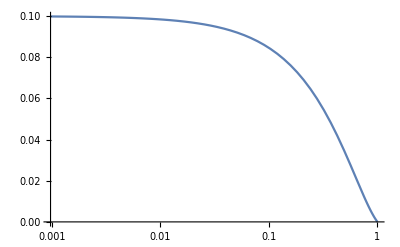

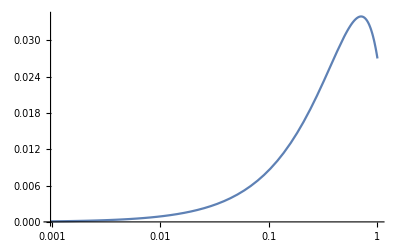

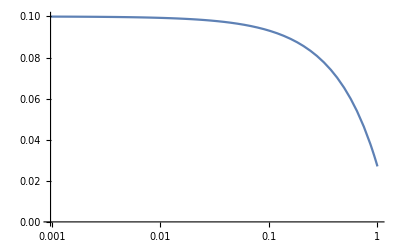

```mathematica
LogLinearPlot[PRc/.qsols[[3]]/.vars/.mvalue/.bv->.55*.9,{v,0,1}]
LogLinearPlot[PRv/.qsols[[3]]/.vars/.mvalue/.bv->.55*.9,{v,0,1}]
LogLinearPlot[(PRv+PRc)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.9,{v,0,1},PlotRange->{0,.1}]
```

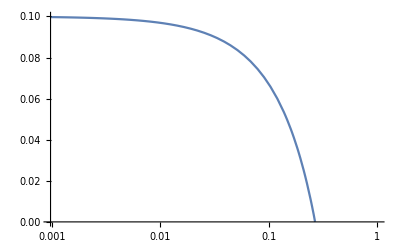

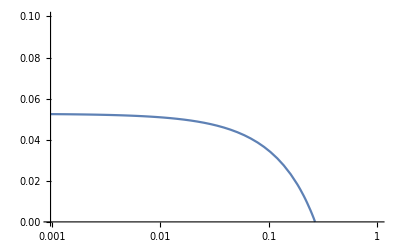

```mathematica
LogLinearPlot[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,{v,0,1},PlotRange->{0,.1}]
LogLinearPlot[PRv/v/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,{v,0,1},PlotRange->{0,.1}]
```

```mathematica
27/41/(37/40.)
```

0.711931

```mathematica
FindRoot[1-Exp[-λ*140]==37/40.,{λ,.02}]
FindRoot[1-Exp[-λ*140]==27/41.,{λ,.02}]
0.00767511/0.018501908324613046
```

{λ→0.0185019}

{λ→0.00767511}

```mathematica
Exp[1.]
```

2.71828

```mathematica
-Log[3/40]/140.
-Log[14/41]/140.
```

0.0185019

0.00767511

```mathematica
vs = {1., 100./300, 100./1000,100./3000,100./10000};
prcs =Table[{vs[[i]],Max[{0,Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,v->vs[[i]]
]}]},{i,1,Length[vs]}]
prvs = Table[{vs[[i]],Max[{0,Limit[PRv/(v)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5,v->vs[[i]]
]}]},{i,1,Length[vs]}]
```

{{1.,0},{0.333333,0},{0.1,0.0670307},{0.0333333,0.0895058},{0.01,0.0969003}}

{{1.,0},{0.333333,0},{0.1,0.0346776},{0.0333333,0.0468496},{0.01,0.0509171}}

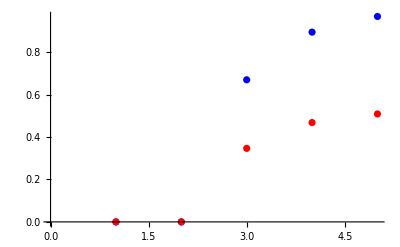

```mathematica
plot1=ListPlot[prcs[[;;,2]]/.1, PlotStyle->Blue];
plot2=ListPlot[prvs[[;;,2]]/.1, PlotStyle->Red];
Show[plot1,plot2]
```

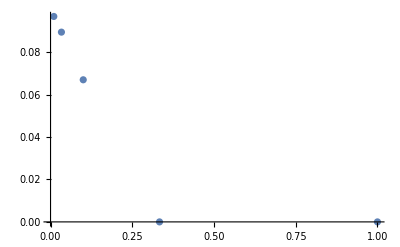

```mathematica
ListPlot[prcs]
```

```mathematica
Solve[(PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.bv->.55*.5)==0,v]
```

{{v→0.26663}}

## An example power calculation

```mathematica
vars={a->0.27,c->0.15,g->0.10536051565782628,n->11,r->0.005,bc->0.55};
```

```mathematica
(* Three parameters: the standard normal distribution values corresponding to upper-tail probabilities of 0.9, 0.8, and 0.025 respectively *)
z90 = 1.28;
z80 = 0.84;
za2 = 1.96;
(* Show, with numerical integration *)
NIntegrate[Exp[-x^2/2]/√(2π),{x,-∞,1.96}]
NIntegrate[Exp[-x^2/2]/√(2π),{x,-∞,1.28}]
NIntegrate[Exp[-x^2/2]/√(2π),{x,-∞,.84}]
```

0.975002

0.899727

0.799546

How many people do we need in each group?

### Let's start with PR = 0.2. 50% coverage, 30% reduction in efficiency

```mathematica
PRv/.(qsols[[3]]/.vars)/.mvalues[[2,1,1]]/.{bv->.7*.55, v->0.5}
PRc/.(qsols[[3]]/.vars)/.mvalues[[2,1,1]]/.{bv->.7*.55, v->0.5}
```

0.0387665

0.0535996

```mathematica
(* This is going to be the expected proportion after treatment *)
Subscript[π, 1]=(PRv + PRc)/.(qsols[[3]]/.vars)/.mvalues[[2,1,1]]/.{bv->.7*.55, v->0.5}
Subscript[π, 0]=0.2
```

0.0923661

0.2

```mathematica
(* This is the number of required individuals in each group, for 80% power *)
n80=(za2 + z80)^2(Subscript[π, 0](1-Subscript[π, 0]) + Subscript[π, 1](1-Subscript[π, 1]))/(Subscript[π, 0]-Subscript[π, 1])^2
(* This is the number of required individuals in each group, for 90% power *)
n90=(za2 + z90)^2(Subscript[π, 0](1-Subscript[π, 0]) + Subscript[π, 1](1-Subscript[π, 1]))/(Subscript[π, 0]-Subscript[π, 1])^2
```

165.011

220.946

```mathematica
(* Calculate the number of clusters required using equation 4 and k = 0.5 *)
k = 0.5;
(*  for 80% power*)
1 + (za2 + z80)^2(Subscript[π, 0](1-Subscript[π, 0])/n80  + Subscript[π, 1](1-Subscript[π, 1])/n80 + k^2(Subscript[π, 0]^2+Subscript[π, 1]^2))/(Subscript[π, 0]-Subscript[π, 1])^2 
(*  for 90% power*)
1 + (za2 + z90)^2(Subscript[π, 0](1-Subscript[π, 0])/n90 + Subscript[π, 1](1-Subscript[π, 1])/n90 + k^2(Subscript[π, 0]^2+Subscript[π, 1]^2))/(Subscript[π, 0]-Subscript[π, 1])^2
```

10.2107

12.994

### Now try PR = 0.2. 80% coverage, 30% reduction in efficiency

```mathematica
PRv/.(qsols[[3]]/.vars)/.mvalues[[2,1,1]]/.{bv->.7*.55, v->0.8}
PRc/.(qsols[[3]]/.vars)/.mvalues[[2,1,1]]/.{bv->.7*.55, v->0.8}
```

0.0118688

0.00421209

```mathematica
(* This is going to be the expected proportion after treatment *)
Subscript[π, 1]=(PRv + PRc)/.(qsols[[3]]/.vars)/.mvalues[[2,1,1]]/.{bv->.7*.55, v->0.8}
Subscript[π, 0]=0.2
```

0.0160809

0.2

```mathematica
(* This is the number of required individuals in each group, for 80% power, using equation 3 *)
n80=(za2 + z80)^2(Subscript[π, 0](1-Subscript[π, 0]) + Subscript[π, 1](1-Subscript[π, 1]))/(Subscript[π, 0]-Subscript[π, 1])^2
(* This is the number of required individuals in each group, for 90% power,using equation 3 *)
n90=(za2 + z90)^2(Subscript[π, 0](1-Subscript[π, 0]) + Subscript[π, 1](1-Subscript[π, 1]))/(Subscript[π, 0]-Subscript[π, 1])^2
```

40.7508

54.5645

```mathematica
(* Calculate the number of clusters required using equation 4 and k = 0.5 *)
k = 0.5;
(*  for 80% power*)
1 + (za2 + z80)^2(Subscript[π, 0](1-Subscript[π, 0])/n80  + Subscript[π, 1](1-Subscript[π, 1])/n80 + k^2(Subscript[π, 0]^2+Subscript[π, 1]^2))/(Subscript[π, 0]-Subscript[π, 1])^2 
(*  for 90% power*)
1 + (za2 + z90)^2(Subscript[π, 0](1-Subscript[π, 0])/n90 + Subscript[π, 1](1-Subscript[π, 1])/n90 + k^2(Subscript[π, 0]^2+Subscript[π, 1]^2))/(Subscript[π, 0]-Subscript[π, 1])^2
```

4.33271

5.12345

## Indirect effect size vs. coverage

```mathematica
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};
```

### Baseline PR = 0.2

```mathematica
(* And here is the m parameter prior to intervention *)
mvalue =Solve[.2 ==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.vars/.b->.55,m][[1]][[1]];
```

Remember : v is the fraction of people vaccinated, or the coverage

```mathematica
(* With 25% efficacy, what is the Parasite Rate in the control group (indirect effect size) *)
{Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
(* Parasite Rate in the vaccinated group? *)
{Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
```

{0.,0.0314438,0.063284,0.10286,0.139136,0.168674,0.18937,0.196792}

{0.00686814,0.0483049,0.0490139,0.0401199,0.027274,0.0147471,0.00514969,0.00156881}

```mathematica
(* With 50% efficacy, what is the Parasite Rate in the control group (indirect effect size) *)
{Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
(* Parasite Rate in the vaccinated group (direct effect size) *)
{Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
```

{0.,0,0.00423353,0.0606485,0.112932,0.155335,0.184882,0.195441}

{0,0,0.00212576,0.0158846,0.0151885,0.00944479,0.00352467,0.00109518}

```mathematica
(* With 75% efficacy, what is the Parasite Rate in the control group (indirect effect size) *)
{Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
(* Parasite Rate in the vaccinated group (direct effect size) *)
{Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
```

{0.,0,0,0.00525711,0.0810361,0.139828,0.179803,0.193927}

{0,0,0,0.000661049,0.00548117,0.0043964,0.00180131,0.00057405}

```mathematica
(* 25% efficacy *)(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0.0943314847683902,0.1265679577142269,0.15428945043481274,0.1739205516706338,0.1874155147120687,0.19589948824323677,0.19877939389896182}/0.2
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0.006868135332592007,0.07245736631297028,0.09802776168459937,0.12035964364420826,0.13636979107679678,0.14747123540627446,0.1544907824894215,0.15688070845973795}/0.2
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0.0943314847683902,0.1265679577142269,0.15428945043481274,0.1739205516706338,0.1874155147120687,0.19589948824323677,0.19877939389896182}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0.006868135332592007,0.07245736631297028,0.09802776168459937,0.12035964364420826,0.13636979107679678,0.14747123540627446,0.1544907824894215,0.15688070845973795}[[i]],{i,1,8}]
```

{Indeterminate,0.0943315,0.126568,0.154289,0.173921,0.187416,0.195899,0.198779}

{0.00686814,0.0724574,0.0980278,0.12036,0.13637,0.147471,0.154491,0.156881}

{0.,0.471657,0.63284,0.771447,0.869603,0.937078,0.979497,0.993897}

{0.0343407,0.362287,0.490139,0.601798,0.681849,0.737356,0.772454,0.784404}

{31.36,172.329,393.36,1089.95,3500.45,15459.8,148052.,1.68003×10^6}

{35.0638,109.503,187.299,328.643,537.873,811.835,1100.14,1232.41}

```mathematica
(* 50% efficacy *)
(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0.00846705383016122,0.09097267784555091,0.141164786104256,0.1725945793045574,0.1912569259218898,0.19741557926749437}/0.2
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0.004251525864257033,0.047653942292917695,0.0759426037601274,0.09444788624894979,0.1057402395414124,0.10951807693271395}/0.2
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0,0.00846705383016122,0.09097267784555091,0.141164786104256,0.1725945793045574,0.1912569259218898,0.19741557926749437}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0,0.004251525864257033,0.047653942292917695,0.0759426037601274,0.09444788624894979,0.1057402395414124,0.10951807693271395}[[i]],{i,1,8}]
```

{Indeterminate,0,0.00846705,0.0909727,0.141165,0.172595,0.191257,0.197416}

{0,0,0.00425153,0.0476539,0.0759426,0.0944479,0.10574,0.109518}

{0.,0.,0.0423353,0.454863,0.705824,0.862973,0.956285,0.987078}

{0.,0.,0.0212576,0.23827,0.379713,0.472239,0.528701,0.54759}

{31.36,31.36,35.9881,160.07,636.963,3160.87,32274.1,373784.}

{31.36,31.36,33.6032,69.3774,117.254,172.776,224.622,246.61}

```mathematica
(* 75% efficacy *)
(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0.007885672357672568,0.10129507987008124,0.15536469105422687,0.1860029263706398,0.19588568405549947}/0.2
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0.001983146924581569,0.027405826506155112,0.04396401439957717,0.054039337823368616,0.057405040187964544}/0.2
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0,0,0.007885672357672568,0.10129507987008124,0.15536469105422687,0.1860029263706398,0.19588568405549947}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0,0,0.001983146924581569,0.027405826506155112,0.04396401439957717,0.054039337823368616,0.057405040187964544}[[i]],{i,1,8}]
```

{Indeterminate,0,0,0.00788567,0.101295,0.155365,0.186003,0.195886}

{0,0,0,0.00198315,0.0274058,0.043964,0.0540393,0.057405}

{0.,0.,0.,0.0394284,0.506475,0.776823,0.930015,0.979428}

{0.,0.,0.,0.00991573,0.137029,0.21982,0.270197,0.287025}

{31.36,31.36,31.36,35.6492,202.009,1146.01,12461.4,147057.}

{31.36,31.36,31.36,32.387,49.125,65.0556,77.6912,82.5551}

```mathematica
(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->0},0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000},bv->0],0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->0},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0,0.05553250626784981,0.13579222500793328,0.18007344914039314,0.1941629295461758}/0.2
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0.,0.,0.,0.,0.,0.,0.,0.}/0.2
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0,0,0,0.05553250626784981,0.13579222500793328,0.18007344914039314,0.1941629295461758}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0.,0.,0.,0.,0.,0.,0.,0.}[[i]],{i,1,8}]
```

{Indeterminate,0,0,0,0.0555325,0.135792,0.180073,0.194163}

{0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.277663,0.678961,0.900367,0.970815}

{0.,0.,0.,0.,0.,0.,0.,0.}

{31.36,31.36,31.36,31.36,79.8049,527.44,6074.42,72819.9}

{31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36}

-0.95574

### Baseline PR = 0.1

```mathematica
(* And here is the m parameter prior to intervention *)
mvalue =Solve[.1 ==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.vars/.b->.55,m][[1]][[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
mvalue
```

m→0.322061

Remember : v is the fraction of people vaccinated, or the coverage

```mathematica
(* With 25% efficacy, what is the Parasite Rate in the control group (indirect effect size) *)
{Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
(* Parasite Rate in the vaccinated group? *)
{Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
```

{0.,0,0.00387264,0.0286634,0.05411,0.0759914,0.0917739,0.0975094}

{0,0,0.00291012,0.0108656,0.0103201,0.00646917,0.00243117,0.000757356}

```mathematica
(* With 50% efficacy, what is the Parasite Rate in the control group (indirect effect size) *)
{Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
(* Parasite Rate in the vaccinated group (direct effect size) *)
{Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
```

{0.,0,0,0,0.0231543,0.0603276,0.0865223,0.0959313}

{0,0,0,0,0.00293679,0.00346776,0.00156165,0.000509171}

```mathematica
(* With 75% efficacy, what is the Parasite Rate in the control group (indirect effect size) *)
{Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRc/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
(* Parasite Rate in the vaccinated group (direct effect size) *)
{Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRv/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
```

{0.,0,0,0,0,0.0431977,0.0809218,0.0942621}

{0,0,0,0,0,0.00124475,0.000744334,0.000256341}

```mathematica
(* 25% efficacy *)(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.75},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.75},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0.007745282319086555,0.04299506049132368,0.06763747222843411,0.08443485976648643,0.09493849347766357,0.09849435171814758}/0.1
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0.005820231573489654,0.032596669310700044,0.05160063835729076,0.06469170355427989,0.07293495376635792,0.07573564715575055}/0.1
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.1/.p1->{0,0,0.007745282319086555,0.04299506049132368,0.06763747222843411,0.08443485976648643,0.09493849347766357,0.09849435171814758}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.1/.p1->{0,0,0.005820231573489654,0.032596669310700044,0.05160063835729076,0.06469170355427989,0.07293495376635792,0.07573564715575055}[[i]],{i,1,8}]
```

{Indeterminate,0,0.00774528,0.0429951,0.0676375,0.0844349,0.0949385,0.0984944}

{0,0,0.00582023,0.0325967,0.0516006,0.0646917,0.072935,0.0757356}

{0.,0.,0.0774528,0.429951,0.676375,0.844349,0.949385,0.984944}

{0.,0.,0.0582023,0.325967,0.516006,0.646917,0.72935,0.757356}

{70.56,70.56,89.9846,316.408,1145.78,5414.03,53837.4,618330.}

{70.56,70.56,84.6651,209.726,465.005,946.495,1686.93,2130.58}

```mathematica
(* 50% efficacy *)
(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.5},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.5},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0,0.02894286138414373,0.06703071598552066,0.08950584764095229,0.09690027884176594}/0.1
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0,0.014683928140443864,0.034677589830247185,0.04684957948205816,0.050917078997201465}/0.1
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.1/.p1->{0,0,0,0,0.02894286138414373,0.06703071598552066,0.08950584764095229,0.09690027884176594}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.1/.p1->{0,0,0,0,0.014683928140443864,0.034677589830247185,0.04684957948205816,0.050917078997201465}[[i]],{i,1,8}]
```

{Indeterminate,0,0,0,0.0289429,0.0670307,0.0895058,0.0969003}

{0,0,0,0,0.0146839,0.0346776,0.0468496,0.0509171}

{0.,0.,0.,0.,0.289429,0.670307,0.895058,0.969003}

{0.,0.,0.,0.,0.146839,0.346776,0.468496,0.509171}

{70.56,70.56,70.56,70.56,183.387,1100.21,12208.8,144842.}

{70.56,70.56,70.56,70.56,112.522,226.867,373.701,450.147}

```mathematica
(* 75% efficacy *)
(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->.55*.25},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->.55*.25},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0,0,0.04799749046997969,0.08371222614183438,0.09521423515777275}/0.1
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0,0,0.012447457665501482,0.022330028854366593,0.025634107762889657}/0.1
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.1/.p1->{0,0,0,0,0,0.04799749046997969,0.08371222614183438,0.09521423515777275}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.1/.p1->{0,0,0,0,0,0.012447457665501482,0.022330028854366593,0.025634107762889657}[[i]],{i,1,8}]
```

{Indeterminate,0,0,0,0,0.0479975,0.0837122,0.0952142}

{0,0,0,0,0,0.0124475,0.02233,0.0256341}

{0.,0.,0.,0.,0.,0.479975,0.837122,0.952142}

{0.,0.,0.,0.,0.,0.124475,0.2233,0.256341}

{70.56,70.56,70.56,70.56,70.56,393.394,4926.52,60296.5}

{70.56,70.56,70.56,70.56,70.56,104.622,145.336,162.997}

```mathematica
(* Fraction sick in the unvaccinated group (indirect effect size) *)
{Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->0},0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/150},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/200},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/300},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/500},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/1000},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/3000},bv->0],0}],
Max[{Limit[PRc/(1-v)/.qsols[[3]]/.vars/.mvalue/.{v->100/10000},bv->0],0}]}
(* Fraction sick in the vaccinated group (direct effect size) *)
{Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/100,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/150,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/200,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/300,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/500,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/1000,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/3000,bv->0},0}],
Max[{PRv/v/.qsols[[3]]/.vars/.mvalue/.{v->100/10000,bv->0},0}]}
(* Indirect Effect size - relative rate of being parasite positive, if vaccinated *)
{0,0,0,0,0.05553250626784981,0.13579222500793328,0.18007344914039314,0.1941629295461758}/0.2
(* Direct Effect size - relative rate of being parasite positive, if vaccinated *)
{0.,0.,0.,0.,0.,0.,0.,0.}/0.2
(* Number of clusters required to obtain 80% power, indirect effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0,0,0,0,0.05553250626784981,0.13579222500793328,0.18007344914039314,0.1941629295461758}[[i]],{i,1,8}]
(* Number of clusters required to obtain 80% power, direct effect *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->.2/.p1->{0.,0.,0.,0.,0.,0.,0.,0.}[[i]],{i,1,8}]
```

{Indeterminate,0,0,0,0.0555325,0.135792,0.180073,0.194163}

{0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.277663,0.678961,0.900367,0.970815}

{0.,0.,0.,0.,0.,0.,0.,0.}

{31.36,31.36,31.36,31.36,79.8049,527.44,6074.42,72819.9}

{31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36}

-0.95574

## Effect size vs. baseline PfPR, with constant coverage and cluster size

```mathematica
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};c
```

```mathematica
(* Range of PR values *)
prvalues = Table[i/50.,{i,1,12}]
(* And here is the m parameter prior to intervention *)
mvalues =Table[Solve[i/50. ==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.vars/.b->.55,m][[1]][[1]],{i,1,12}]
```

{m→0.287011,m→0.295226,m→0.30379,m→0.312727,m→0.322061,m→0.331819,m→0.34203,m→0.352729,m→0.363949,m→0.37573,m→0.388115,m→0.401152}

### 75 % coverage, 50 % effective vaccine

```mathematica
(* Direct effect sizes *)
deff=Table[Max[{PRv/v/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->150/200,bv->.55*.5},0}],{i,1,Length[mvalues]}]
(* Indirect effect sizes *)
ideff = Table[Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->150/200,bv->.55*.5},0}],{i,1,Length[mvalues]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* For measuring direct (or indirect) effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->0,{i,1,Length[prvalues]}]
```

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,35.7156,31.36,27.7964,24.8267}

### 75 % coverage, 25 % effective vaccine

```mathematica
(* Direct effect sizes *)
deff=Table[Max[{PRv/v/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->150/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
(* Indirect effect sizes *)
ideff = Table[Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->150/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
```

{0,0,0,0,0,0,0,0.0173112,0.0376615,0.0581536,0.0787879,0.0995649}

{0,0,0,0,0,0,0,0.0229491,0.0495928,0.0760637,0.102362,0.128489}

```mathematica
(* For measuring direct effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->deff[[i]],{i,1,Length[prvalues]}]
(* For measuring indirect effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->ideff[[i]],{i,1,Length[prvalues]}]
```

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,58.3035,71.1408,83.6867,96.0025,108.147}

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,65.4577,89.7746,117.536,149.271,185.604}

### 90% coverage, 25 % effective vaccine

```mathematica
(* Direct effect sizes *)
deff=Table[Max[{PRv/v/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->180/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
(* Indirect effect sizes *)
ideff = Table[Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->180/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
```

{0,0,0,0,0,0,0,0,0.00724912,0.0291463,0.0511562,0.0732791}

{0,0,0,0,0,0,0,0,0.00964219,0.0384878,0.0670647,0.0953758}

```mathematica
(* For measuring direct effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->deff[[i]],{i,1,Length[prvalues]}]
(* For measuring indirect effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->ideff[[i]],{i,1,Length[prvalues]}]
```

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,40.6665,50.572,60.5402,70.6013}

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,42.4526,59.2088,78.4922,100.709}

### 95% coverage, 25 % effective vaccine

```mathematica
(* Direct effect sizes *)
deff=Table[Max[{PRv/v/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->190/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
(* Indirect effect sizes *)
ideff = Table[Max[{PRc/(1-v)/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->190/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
```

{0,0,0,0,0,0,0,0,0,0.018347,0.0409024,0.063556}

{0,0,0,0,0,0,0,0,0,0.024314,0.0538029,0.0829833}

```mathematica
(* For measuring direct effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->deff[[i]],{i,1,Length[prvalues]}]
(* For measuring indirect effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->ideff[[i]],{i,1,Length[prvalues]}]
```

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,35.7156,42.2938,51.5309,60.9211}

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,35.7156,46.6665,63.1561,82.2015}

### 100% coverage, 25 % effective vaccine

```mathematica
(* Direct effect sizes *)
deff=Table[Max[{PRv/v/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->200/200,bv->.55*.75},0}],{i,1,Length[mvalues]}]
```

{0,0,0,0,0,0,0,0,0,0.00686814,0.0300247,0.0532614}

```mathematica
(* For measuring direct effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->deff[[i]],{i,1,Length[prvalues]}]
```

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,35.7156,35.0638,43.6033,52.3452}

### 100% coverage, 30 % effective vaccine

```mathematica
(* Direct effect sizes *)
deff=Table[Max[{PRv/v/.qsols[[3]]/.vars/.mvalues[[i]]/.{v->200/200,bv->.55*.70},0}],{i,1,Length[mvalues]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0.00433254}

```mathematica
(* For measuring direct effect sizes *)
Table[(1.96 +0.84)^2(p1*(1-p1)+p0*(1-p0))/((p1-p0)^2)/.p0->prvalues[[i]]/.p1->deff[[i]],{i,1,Length[prvalues]}]
```

{384.16,188.16,122.827,90.16,70.56,57.4933,48.16,41.16,35.7156,31.36,27.7964,26.3568}

## Single run through of full methodology

```mathematica
(* Parameters *)
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};
```

```mathematica
(* Calibration *)
mvalue = Solve[0.1==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.b->bc/.vars,m]//Flatten
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{m→0.322061}

```mathematica
(* This gives us the effect sizes *)
effectSizes = qsols/.{bv->.5*.55, v->.9}/.vars/.mvalue
```

{{PRv→0,PRc→0,EIR→0},{PRv→-1.34597,PRc→0.603615,EIR→-0.010896},{PRv→-0.254163,PRc→-0.078708,EIR→-0.00400389}}

```mathematica
(* Use the effect sizes to calculate the number of people needed in an ordinary randomized trial *)
z90 = 1.28;
za2 = 1.96;
Subscript[π, 1] = 0;
Subscript[π, 0]=0.1;
n90=(za2 + z90)^2(Subscript[π, 0](1-Subscript[π, 0]) + Subscript[π, 1](1-Subscript[π, 1]))/(Subscript[π, 0]-Subscript[π, 1])^2
```

94.4784

```mathematica
(* And the necessary number of clusters *)
k = 0.5;
1 + (za2 + z90)^2(Subscript[π, 0](1-Subscript[π, 0])/n90 + Subscript[π, 1](1-Subscript[π, 1])/n90 + k^2(Subscript[π, 0]^2+Subscript[π, 1]^2))/(Subscript[π, 0]-Subscript[π, 1])^2
```

4.6244

So we' ll need at least 5 clusters in each arm with at least 95 people to have a 90% chance to detect a direct effect with at least 95% p-value

## Single Cluster Elimination

```mathematica
q = {PRv == v*bv*EIR/(bv*EIR + r),
PRc == (1-v)*bc*EIR/(bc*EIR + r),
EIR == m a^2 c (PRv + PRc) Exp[-g n]/(a c (PRv + PRc)+g)};
qsols = Solve[q,{PRv, PRc, EIR}];
```

```mathematica
mvalues =Table[Solve[i/10.==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}],{i,1,9}];
```

```mathematica
vars={a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55};
```

```mathematica
PRc/.(qsols[[3]]/.vars)
```

```mathematica
(* Pete says 40% of time in 100% of people in Burkina Faso Trial 

So if we have 100% coverage, then we've essentially reduced the susceptible population to 60% of its original size

(40%, 50%, 60%, 70%) - try these, see whether we can get elimination in a cluster
*)

(* Basupu: has 2000 people,with 12% average PfPR? *)
Solve[.21==(a^2 b c m-ⅇ^(g n) g r)/(a^2 b c m+a c ⅇ^(g n) r)/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,b->.55}][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{m→0.381844}

```mathematica
PRv/.(qsols[[3]]/.vars)/.{m->0.381844069261645}/.{v->.4,bv->0}
Limit[PRc/.(qsols[[3]]/.vars)/.{m->0.381844069261645}/.{v->.4},bv->0]
Limit[PRc/.(qsols[[3]]/.vars)/.{m->0.381844069261645}/.{v->.3},bv->0]
Limit[PRc/.(qsols[[3]]/.vars)/.{m->0.381844069261645}/.{v->.2},bv->0]
Limit[PRc/.(qsols[[3]]/.vars)/.{m->0.381844069261645}/.{v->.1},bv->0]
```

0.

-0.102259

-0.024194

0.0538707

0.131935

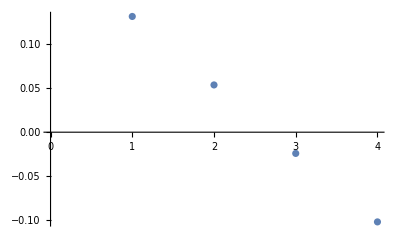

```mathematica
ListPlot[{0.13193533997580054,0.05387067995160122,-0.02419398007259832,-0.10225864009679775}]
```

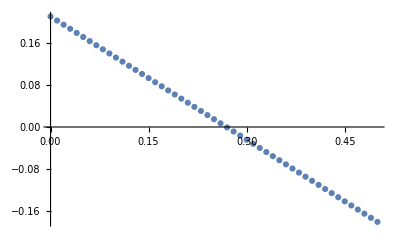

```mathematica
ListPlot[Table[{x, Limit[PRc/.(qsols[[3]]/.vars)/.{m->0.381844069261645}/.{v->x},bv->0]},{x,0,.5,.01}]]
```

```mathematica
(* Just checking *)
q = {PRc == (1-v)*bc*EIR/(bc*EIR + r),
EIR == m a^2 c ( PRc) Exp[-g n]/(a c (PRc)+g)};
Solve[q/.v->0,{PRc, EIR}]
```

{{PRc→0,EIR→0},{PRc→(a^2 bc c m-ⅇ^(g n) g r)/(a c (a bc m+ⅇ^(g n) r)),EIR→(a^2 bc c ⅇ^(-g n) m-g r)/(a bc c+bc g)}}

```mathematica
mvalue =Solve[.2==(a^2 bc c m-ⅇ^(g n) g r)/(a c (a bc m+ⅇ^(g n) r))/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{m→0.37573}

```mathematica
q/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalue
Simplify[Solve[q/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalue,{PRc, EIR}]]
```

{PRc==(0.55 EIR (1-v))/(0.005+0.55 EIR),EIR==(0.00184183 PRc)/(0.105361+0.0405 PRc)}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{PRc→0.,EIR→0.},{PRc→0.4-0.833402 v,EIR→(0.0218272-0.0454772 v)/(3.60149-1. v)}}

```mathematica
Simplify[-7.332923242061753*^-17 (-2.863796511539041*^15+1.064577624056112*^16 v)]
```

0.21-0.780647 v

```mathematica
(* v = fraction of population protected by the vaccine *)
```

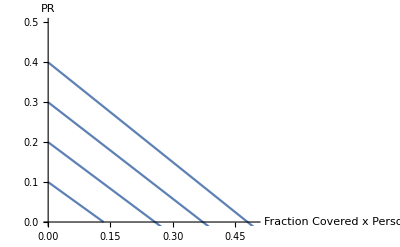

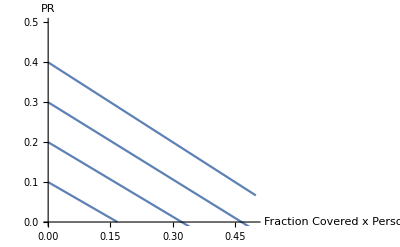

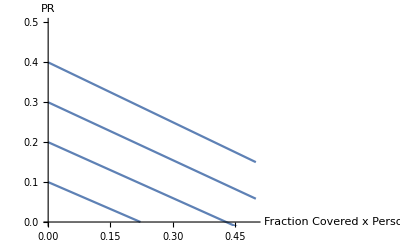

```mathematica
p1 = Plot[0.1-0.7501037217946771 v,{v,0,.5},
PlotRange->{{0,.5},{0,.5}},
AxesLabel->{"Fraction Covered x Personal Protective Efficacy","PR"}];
p2 = Plot[0.2-0.7778699749286021 v,{v,0,.5}];
p3 = Plot[0.3-0.8056362280625267 v,{v,0,.5}];
p4 = Plot[0.4-0.8334024811964516 v,{v,0,.5}];
Show[{p1, p2, p3, p4}]

p1 = Plot[0.1-0.7501037217946771*.8v,{v,0,.5},
PlotRange->{{0,.5},{0,.5}},
AxesLabel->{"Fraction Covered x Personal Protective Efficacy","PR"}];
p2 = Plot[0.2-0.7778699749286021 *.8v,{v,0,.5}];
p3 = Plot[0.3-0.8056362280625267 *.8v,{v,0,.5}];
p4 = Plot[0.4-0.8334024811964516 *.8v,{v,0,.5}];
Show[{p1, p2, p3, p4}]

p1 = Plot[0.1-0.7501037217946771*.6v,{v,0,.5},
PlotRange->{{0,.5},{0,.5}},
AxesLabel->{"Fraction Covered x Personal Protective Efficacy","PR"}];
p2 = Plot[0.2-0.7778699749286021 *.6v,{v,0,.5}];
p3 = Plot[0.3-0.8056362280625267 *.6v,{v,0,.5}];
p4 = Plot[0.4-0.8334024811964516 *.6v,{v,0,.5}];
Show[{p1, p2, p3, p4}]
```

```mathematica
(* And a companion plot: when do we hit zero? *)
```

```mathematica
mvalues =Table[Solve[i==(a^2 bc c m-ⅇ^(g n) g r)/(a c (a bc m+ⅇ^(g n) r))/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}][[1]],{i,.025,.95,.025}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{m→0.289033},{m→0.299463},{m→0.310456},{m→0.322061},{m→0.334328},{m→0.347317},{m→0.361093},{m→0.37573},{m→0.391311},{m→0.407931},{m→0.425698},{m→0.444733},{m→0.465179},{m→0.487197},{m→0.510977},{m→0.536738},{m→0.564739},{m→0.595286},{m→0.628742},{m→0.665544},{m→0.70622},{m→0.751415},{m→0.801927},{m→0.858754},{m→0.923157},{m→0.996761},{m→1.08169},{m→1.18077},{m→1.29787},{m→1.43838},{m→1.61012},{m→1.8248},{m→2.10082},{m→2.46883},{m→2.98406},{m→3.7569},{m→5.04496},{m→7.62109}}

```mathematica
Table[v/.Solve[(PRc/.Solve[q/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalues[[i]],{PRc, EIR}][[2]]) == 0,v][[1]],{i,1,Length[mvalues]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{0.0342804,0.0679144,0.10092,0.133315,0.165116,0.196338,0.226999,0.257112,0.286693,0.315755,0.344312,0.372377,0.399962,0.42708,0.453742,0.47996,0.505745,0.531108,0.556058,0.580606,0.604762,0.628534,0.651932,0.674965,0.697641,0.719968,0.741954,0.763608,0.784935,0.805945,0.826644,0.847038,0.867135,0.886941,0.906461,0.925703,0.944673,0.963375}

```mathematica
Solve[0==PRc/.Solve[q/.{a->.3*.9, c->.15, g->-Log[.9], n->11, r->1./200,bc->.55}/.mvalue,{PRc, EIR}][[2]],v][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{v→0.257112}

```mathematica
Solve[0.2-0.7778699749286021 v==0 ,v]
Solve[0.2-0.7778699749286021 v*.8==0 ,v]
Solve[0.2-0.7778699749286021 v*.6==0 ,v]
```

{{v→0.257112}}

{{v→0.32139}}

{{v→0.428521}}

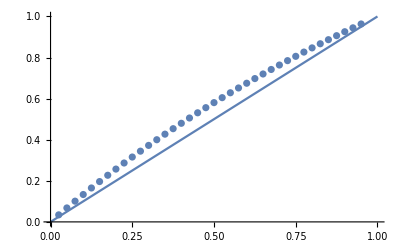

```mathematica
Show[{Plot[x,{x,0,1}],ListPlot[Transpose[{Table[i,{i,.025,.95,.025}],{0.034280431638560704,0.06791442717591284,0.10092010087038097,0.13331489645291028,0.1651156178683484,0.19633845834083805,0.22699902786895507,0.257112379248675,0.2866930327153233,0.3157549992892583,0.34431180290415137,0.3723765013912912,0.3999617063883181,0.4270796022361638,0.45374196392368193,0.47996017413549213,0.5057452394548968,0.5311078057703215,0.5560581729305865,0.5806063086913946,0.6047618619927076,0.6285341756041658,0.6519322981733677,0.6749649957096504,0.6976407625339861,0.7199678317237345,0.741954185079225,0.7636075626375177,0.7849354717571669,0.8059451957963821,0.8266438024056683,0.8470381514547697,0.8671349026126047,0.8869405225977781,0.9064612921162555,0.9257033125018388,0.9446725120741842,0.9633746522282888}}],PlotRange->{{0,1},{0,1}}]}]
```